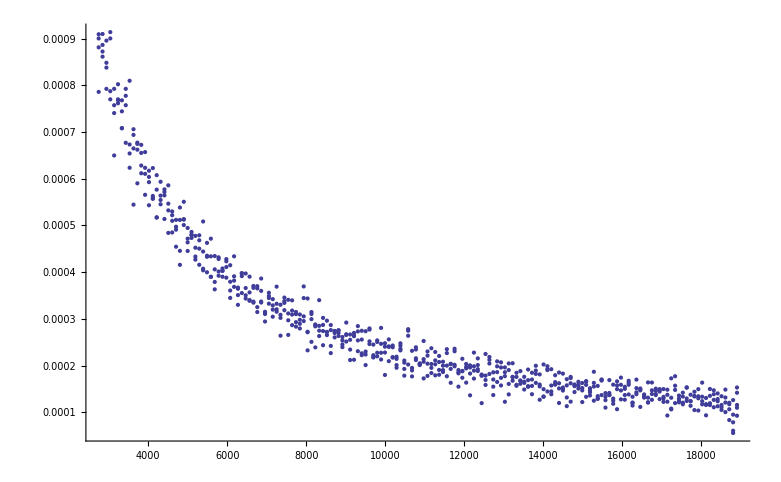

```mathematica
datalist={};DynamicModule[{k=0,a=0,x=95.,MolList=Table[{RandomReal[{-45,45},{2}],.3{Cos[#],Sin[#]}&[RandomReal[{0,2Pi}]]},{50}],Force=0,Pressure=0,Volume=0.},
Column[{
Column[{Slider[Dynamic[x],{-70,95}],Row[{"Volume = ",Dynamic[ScientificForm[Volume,3]]}],Row[{"Pressure = ",Dynamic[ScientificForm[Pressure,3]]}]
}],
Graphics[{{Brown,Polygon[Dynamic[{{50+x,50},{55+x,50},{55+x,-50},{50+x,-50}}]]},{Polygon[{{150,-50},{-50,-50},{-50,50},{150,50},{150,55},{-55,55},{-55,-55},{150,-55}}]},{PointSize[.01],Point[Dynamic[k++;
MolList=Map[{{Min[#[[1,1]]+#[[2,1]],49+x],#[[1,2]]+#[[2,2]]},{If[!(-49<=#[[1,1]]+#[[2,1]]<=49+x),Force+=2Abs[#[[2,1]]];-Sign[#[[1,1]]+40],Sign[#[[2,1]]]],If[Abs[#[[1,2]]+#[[2,2]]]≥49,Force+=2Abs[#[[2,2]]];-Sign[#[[1,2]]],Sign[#[[2,2]]]]}Abs[#[[2]]]}&,MolList];
Volume=((100-2)*(100+x-2));
If[Mod[k,210]==0,Pressure=(Force/210)/(100-2+100-2+2(100+x-2));AppendTo[datalist,{Pressure,Volume}];Force=0];
Do[Do[If[Norm[MolList[[y,1]]-MolList[[x,1]]]<2,MolList=ReplacePart[MolList,{y->{(MolList[[x,1]]+MolList[[y,1]])/2-Normalize[MolList[[x,1]]-MolList[[y,1]]],Projection[MolList[[y,2]]-MolList[[x,2]],{-1,1}Reverse[MolList[[x,1]]-MolList[[y,1]]]]+MolList[[x,2]]},
x->{(MolList[[x,1]]+MolList[[y,1]])/2+Normalize[MolList[[x,1]]-MolList[[y,1]]],Projection[MolList[[y,2]]-MolList[[x,2]],MolList[[x,1]]-MolList[[y,1]]]+MolList[[x,2]]}
}]],{y,x+1,Length[MolList]}],{x,1,Length[MolList]-1}];Pressure*Volume;Map[First,MolList]]]}},PlotRange->{{-55,150},{-55,55}},Axes->False,Background->LightGray,ImageSize->800]}]]
```